```mathematica
SetDirectory["D:\\phd_projects\\NTU\\NbSe2\\nbse2_band"];
```

```mathematica
t0[1]=10.9/1000;
t1[1]=86.8/1000;
t2[1]=139.9/1000;
t3[1]=29.6/1000;
t4[1]=3.5/1000;
t5[1]=3.3/1000;

t0[2]=203.0/1000;
t1[2]=46.0/1000;
t2[2]=257.5/1000;
t3[2]=4.4/1000;
t4[2]=−15.0/1000;
t5[2]=6.0/1000;
```

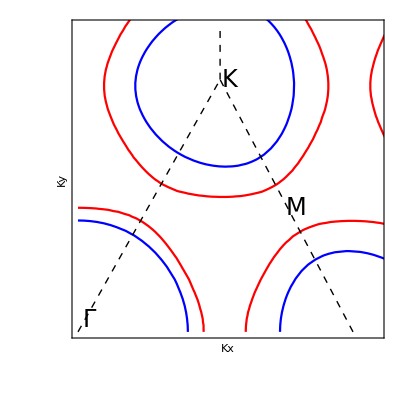

```mathematica
Clear[kx,ky];
For[i=1,i≤2,i++,
ξ=(1/2)kx*a;
η=(1/2)Sqrt[3]*ky*a;
a=3.444;
e[i]=(t0[i]+t1[i] (2 Cos[ξ]Cos[η]+Cos[ 2ξ])+t2[i] (2Cos[3ξ]Cos[η]+Cos[2η])+t3 [i](2Cos[2ξ]Cos[2η]+Cos[4ξ])+t4 [i](Cos[ξ]Cos[3η]+Cos[5ξ]Cos[η]+Cos[4ξ]Cos[2η])+t5 [i](2Cos[3ξ]Cos[3η]+Cos[6ξ]))
];
f=ContourPlot[{e[1]==0.0,e[2]==0.0},{kx,0,Pi},{ky,0,Pi},FrameLabel->{"Kx","Ky"},ContourStyle->{Blue,Red},
FrameStyle->Directive[Black,Thick],FrameTicksStyle->Black,ImageSize->400,LabelStyle->{FontFamily->"Times New Roman",Black,FontSize->24},
FrameTicks -> {{None, None}, {None, None}},PlotRange->{{0,Pi/2.4},{0,Pi/2.4}},(*Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},*)AspectRatio->1];
g=Graphics[{Thick,Black,Dashed,Line[{{0,0},{0.62,1.08}}],Line[{{1.2,0.0},{0.62,1.08}}],Line[{{0.62,1.08},{0.62,1.3}}]}];
h1=Graphics[Text[Style[Γ,FontFamily->"Times New Roman",Black,FontSize->24],{0.05,0.05}]];
h2=Graphics[Text[Style["K",FontFamily->"Times New Roman",Black,FontSize->24],{0.66,1.08}]];
h3=Graphics[Text[Style["M",FontFamily->"Times New Roman",Black,FontSize->24],{0.95,0.53}]];
pl=Show[f,g,h1,h2,h3]
```

```mathematica
Export["fermi.png",Rasterize[pl,ImageResolution->300]]
```

fermi.png

```mathematica
Export["fermi.eps",pl]
```

fermi.eps

```mathematica
(*kx=0;
ky=0;
(e[1]+e[2])/2*)
```

```mathematica
p=200;
(*For[j=0,j≤100,j++,*)
ky=-kx/Sqrt[3];
tabgm1=Table[e[1],{kx,0,Pi/a,Pi/(p*a)}];
tabgm2=Table[e[2],{kx,0,Pi/a,Pi/(p*a)}];
ky=kx*Sqrt[3]-4*Pi/(Sqrt[3]*a);
tabmk1=Table[e[1],{kx,Pi/(a),4Pi/(3a),4Pi/(3a*p)}];
tabmk2=Table[e[2],{kx,Pi/(a),4Pi/(3a),4Pi/(3a*p)}];
ky=0;
tabkg1=Table[e[1],{kx,4Pi/(3*a),0,-4Pi/(3*a*p)}];
tabkg2=Table[e[2],{kx,4Pi/(3*a),0,-4Pi/(3*a*p)}];
```

```mathematica
tabgg1=Join[tabgm1,tabmk1, tabkg1];
tabgg2=Join[tabgm2,tabmk2, tabkg2];
Dimensions[tabgm1]
Dimensions[tabmk1]
Dimensions[tabkg1]
Dimensions[tabgg1]
```

{201}

{51}

{201}

{453}

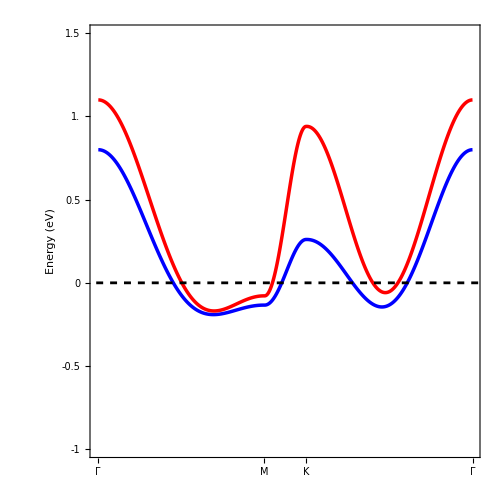

```mathematica
plot=ListPlot[{tabgg1,tabgg2},Frame->True,ImageSize->500,FrameStyle->Directive[Black,Thick],LabelStyle->{FontFamily->"Times New Roman",Black,FontSize->24},
PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]}},FrameLabel->{"","Energy (eV)"},PlotTheme->"Detailed",Joined->True,(*PlotMarkers->{Automatic,3},*)
FrameTicks -> {{{-1,-0.5,0,0.5,1.0,1.5}, None}, {{{0, "Γ",{0.6,0}}, {201, "M",{1,0}},{252, "K",{1,0}},{453, "Γ",{0.6,0}}}, {None}}},
(*Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},*)AspectRatio->1,PlotRange->{{0,453},{-1,1.5}},GridLines->{None,{0}},GridLinesStyle->Directive[Black,Thickness[0.004],Dashed]]
```

```mathematica
Export["nbse2_band.png",Rasterize[plot,ImageResolution->300]]
```

nbse2_band.png

```mathematica
Export["nbse2_band.eps",plot]
```

nbse2_band.eps

```mathematica
Export["nbse2_band_2.dat",tabgg2]
```

nbse2_band_2.dat

```mathematica
(*ky=0;
Plot[{e[1],e[2]},{kx,0,4Pi/a},Frame->True]*)
```

```mathematica
(*Clear[kx,ky];
i=0;
n=200;

For[ky=0,ky<=4Pi/(Sqrt[3]*a),ky+=4/Sqrt[3]Pi/(a*n),
For[kx=0,kx≤4Pi/a,kx+=4Pi/(a*n),
For[m=1,m≤2,m++,
If[
e[m]≤-0.0006,i=i+1;
]]]]
Print["  Ratio=",N[i/n^2/2]]*)
```

```mathematica
(**)
```